```mathematica
time={{1 ,33.837660},{2 ,8.926943},{4,9.832782},{8 ,4.159676},{16, 1.883718},{32, 0.920974},{64 ,0.485961}};
```

```mathematica
timeR=Table[{time[[i,1]],1/time[[i,2]]},{i,Length[time]}]
```

{{1,0.0295529},{2,0.11202},{4,0.101701},{8,0.240403},{16,0.530865},{32,1.08581},{64,2.05778}}

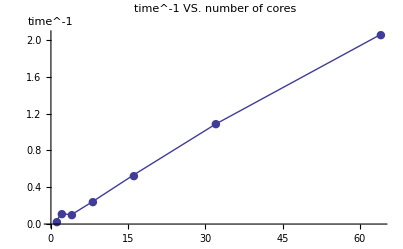

```mathematica
ListPlot[timeR,Joined->True,PlotMarkers->{Automatic,Medium},PlotLabel->"time^-1 VS. number of cores", AxesLabel->{"", "time^-1"}]
```

```mathematica
time2={{1, 11.775532},{2, 8.025935},{4, 7.340342},{8, 5.410584},{16, 2.841941},{32, 1.474556},{64, 0.821028}};
timeR2=Table[{time2[[i,1]],1/time2[[i,2]]},{i,Length[time]}]
```

{{1,0.0849219},{2,0.124596},{4,0.136233},{8,0.184823},{16,0.351872},{32,0.67817},{64,1.21799}}

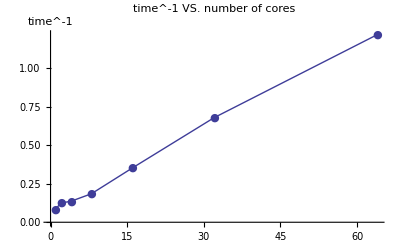

```mathematica
ListPlot[timeR2,Joined->True,PlotMarkers->{Automatic,Medium},PlotLabel->"time^-1 VS. number of cores", AxesLabel->{"", "time^-1"}]
```

```mathematica
gflops={{1,1.8},{2,2.3},{4,2.5},{8,3.3},{16,6.3},{32,12.7},{64,24.7}};
```

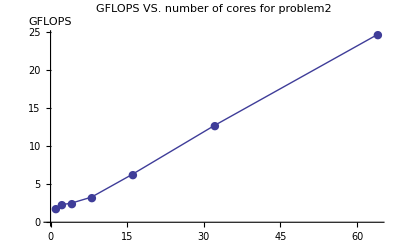

```mathematica
ListPlot[gflops,Joined->True,PlotMarkers->{Automatic,Medium},PlotLabel->"GFLOPS VS. number of cores for problem2", AxesLabel->{"", "GFLOPS"}]
```